## Free trajectory phase

give kick wait until overlapped then interfere

```mathematica
x[t_]:=v0/ω Sin[ω t]
assum={v0∈Reals,m∈Reals,ω∈Reals,ω>0}
x[t]
x'[t]
```

{v0∈ℝ,m∈ℝ,ω∈ℝ,ω>0}

(v0 Sin[t ω])/ω

v0 Cos[t ω]

```mathematica
period = (2π)/ω;
Lagrangian [t_]:=Simplify[ 1/2 m (x'[t])^2- 1/2 m ω^2 (x[t])^2,Assumptions->assum]
Lagrangian[t]
```

1/2 m v0^2 Cos[2 t ω]

```mathematica
action=Integrate[Lagrangian[t],{t,0,period/8},Assumptions->assum]
N[action/.{p->1,m->1,ω->1}]
```

(m v0^2)/(4 ω)

0.25 v0^2

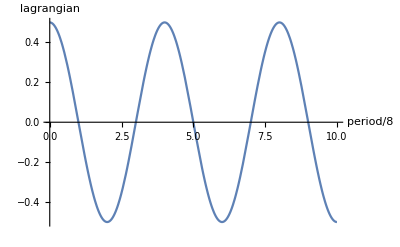

```mathematica
Plot[Lagrangian[t*period/8]/.{v0->1,m->1,ω->1},{t,0,10},AxesLabel->{"period/8","lagrangian"}]
```

## Double kick phase

give kick wait some arb time t1 then kick again

```mathematica
x[t_]:=v0/ω Sin[ω t]
```